```mathematica
(* MKM 505E - Advanced Control Methods in Mechatronics - Final Exam *)
```

```mathematica
(* Mertcan Kaya (518192004) *)
```

```mathematica
(* Transfer function of a 2x2 MIMO system *)
```

```mathematica
tf=TransferFunctionModel[{{(s+3)/((s+1)(s+6)), 1/(6s+1)},{(s+1)/(s^2+11s+100),2/(2s+1)}},s]
```

(3+s)/((1+s) (6+s))1/(1+6 s)(1+s)/(100+11 s+s^2)2/(1+2 s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s2231121110011FalseFalseFalseAutomaticNoneAutomatic

```mathematica
Gs=tf[s];
```

```mathematica
MatrixForm[Gs]
```

((3+s)/((1+s) (6+s)) | 1/(1+6 s)
(1+s)/(100+11 s+s^2) | 2/(1+2 s))

```mathematica
(* i) Determine the relative gain array *)
```

```mathematica
(* R(s) = G(s) o G(s)^(-T) *)
```

```mathematica
Rs=Gs*Inverse[Transpose[Gs]];
```

```mathematica
(* R(s) s->0 evaluated at zero frequency *)
```

```mathematica
R0=Rs/.s->0;
```

```mathematica
MatrixForm[N[R0]]
```

(1.0101 | -0.010101
-0.010101 | 1.0101)

```mathematica
(* pair input 1 to one of the outputs *)
```

```mathematica
If[R0[[1,1]]>0&&(Abs[(R0[[1,1]]-1)]<Abs[(R0[[1,2]]-1)]),u1=y1,If[R0[[1,2]]>0&&(Abs[(R0[[1,2]]-1)]<Abs[(R0[[1,1]]-1)]),u1=y2,u1=error]]
```

y1

```mathematica
(* u1=y1, input one is paired with output one *)
```

```mathematica
(* pair input 2 to one of the outputs *)
```

```mathematica
If[R0[[2,1]]>0&&(Abs[(R0[[2,1]]-1)]<Abs[(R0[[2,2]]-1)]),u2=y1,If[R0[[2,2]]>0&&(Abs[(R0[[2,2]]-1)]<Abs[(R0[[2,1]]-1)]),u2=y2,u2=error]]
```

y2

```mathematica
(* u2=y2, input two is paired with output two *)
```

```mathematica
(* ii) Plot the Nyquist array including the Gershgorin circles with the criteria of row dominance *)
```

```mathematica
(* The Inverse Nyquist Approach *)
```

```mathematica
N[Det[Gs/.s->0]]
```

0.99

```mathematica
(* |G(0)| ≠ 0, so K^(-1)=G(0) is valid approach *)
```

```mathematica
Kinv=Gs/.s->0;
```

```mathematica
MatrixForm[N[Kinv]]
```

(0.5 | 1.
0.01 | 2.)

```mathematica
Ks=Inverse[Kinv];
```

```mathematica
MatrixForm[N[Ks]]
```

(2.0202 | -1.0101
-0.010101 | 0.505051)

```mathematica
(* Q^(-1) = K^(-1) G^(-1) *)
```

```mathematica
Qinv=Simplify[Kinv.Inverse[Gs]];
```

```mathematica
MatrixForm[Qinv]
```

(-((1+s) (6+s) (1+6 s) (-99-8 s+s^2))/(594+3841 s+1590 s^2+153 s^3+10 s^4) | (s (1+2 s) (31+11 s) (100+11 s+s^2))/(1188+7682 s+3180 s^2+306 s^3+20 s^4)
-(s (1+s) (6+s) (1+6 s) (289+199 s))/(50 (594+3841 s+1590 s^2+153 s^3+10 s^4)) | ((1+2 s) (100+11 s+s^2) (594+3793 s+1199 s^2))/(100 (594+3841 s+1590 s^2+153 s^3+10 s^4)))

```mathematica
Qinv0=Qinv/.s->0;
```

```mathematica
MatrixForm[N[Qinv0]]
```

(1. | 0.
0. | 1.)

```mathematica
(* Nyquist Plot for the system *)
```

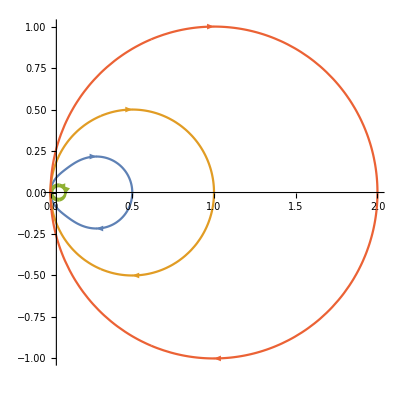

```mathematica
NyquistPlot[Gs]
```

```mathematica
QinvIw=Qinv/.s->(w I);
```

```mathematica
(* G(s) -> G(jw) *)
```

```mathematica
GIw=Gs/.s->(w I);
```

```mathematica
(* The Nyquist Array including the Gershgorin circles with row dominance *)
```

```mathematica
(* Nyquist Array Plot for element {1,1}, first diagonal *)
```

```mathematica
(* f1 = x1 + r1 Cos[t], y1 + r1 Sin[t] *)
```

```mathematica
(* x1 = Re[G11(jw)], y1 = Im[G11(jw)], r1 = dR1, dR1 = |q12(jw)| *)
```

```mathematica
f1w={Re[GIw[[1,1]]]+Abs[QinvIw[[1,2]]] Cos[t],Im[GIw[[1,1]]]+Abs[QinvIw[[1,2]]]  Sin[t]};
```

```mathematica
f11=f1w/.w->0.0;
```

```mathematica
f12=f1w/.w->0.2;
```

```mathematica
f13=f1w/.w->0.4;
```

```mathematica
f14=f1w/.w->0.6;
```

```mathematica
f15=f1w/.w->0.8;
```

```mathematica
f16=f1w/.w->1.0;
```

```mathematica
f17=f1w/.w->1.2;
```

```mathematica
f18=f1w/.w->1.4;
```

```mathematica
f19=f1w/.w->1.6;
```

```mathematica
f110=f1w/.w->1.8;
```

```mathematica
p11=NyquistPlot[Gs[[1,1]]];
```

```mathematica
p12=ParametricPlot[{f11,f12,f13,f14,f15,f16,f17,f18,f19,f110},{t,0,2 Pi}];
```

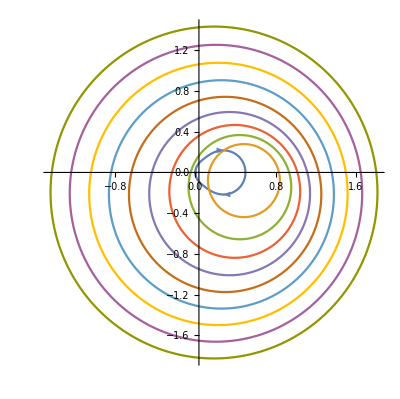

```mathematica
Show[p11,p12,PlotRange->All]
```

```mathematica
(* The Nyquist Array including the Ostrowski circles with row dominance *)
```

```mathematica
(* x1 = Re[G11(jw)], y1 = Im[G11(jw)], r1 = phi1*dR1, phi1 = d2/|1+q22(jw)|, dR1 = |q12(jw)| *)
```

```mathematica
r1=(QinvIw[[2,1]]/Abs[1+QinvIw[[2,2]]])QinvIw[[1,2]];
```

```mathematica
(* Nyquist Array Plot for element {1,2} *)
```

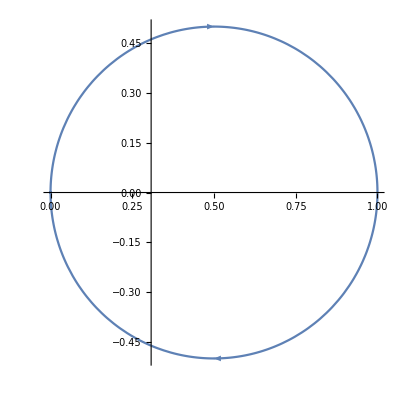

```mathematica
NyquistPlot[Gs[[1,2]]]
```

```mathematica
(* Nyquist Array Plot for element {2,1} *)
```

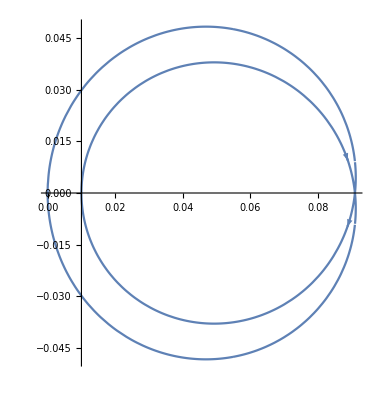

```mathematica
NyquistPlot[Gs[[2,1]]]
```

```mathematica
(* Nyquist Array Plot for element {2,2}, second diagonal *)
```

```mathematica
(* f2 = x2 + r2 Cos[t], y2 + r2 Sin[t] *)
```

```mathematica
(* x2 = Re[G22(jw)], y2 = Im[G22(jw)], r2 = dR2, dR2 = |q21(jw)| *)
```

```mathematica
f2w={Re[GIw[[2,2]]]+Abs[QinvIw[[2,1]]] Cos[t],Im[GIw[[2,2]]]+Abs[QinvIw[[2,1]]]  Sin[t]};
```

```mathematica
f21=f2w/.w->0.0;
```

```mathematica
f22=f2w/.w->0.2;
```

```mathematica
f23=f2w/.w->0.4;
```

```mathematica
f24=f2w/.w->0.6;
```

```mathematica
f25=f2w/.w->0.8;
```

```mathematica
f26=f2w/.w->1.0;
```

```mathematica
f27=f2w/.w->1.2;
```

```mathematica
f28=f2w/.w->1.4;
```

```mathematica
f29=f2w/.w->1.6;
```

```mathematica
f210=f2w/.w->1.8;
```

```mathematica
p21=NyquistPlot[Gs[[2,2]]];
```

```mathematica
p22=ParametricPlot[{f21,f22,f23,f24,f25,f26,f27,f28,f29,f210},{t,0,2 Pi}];
```

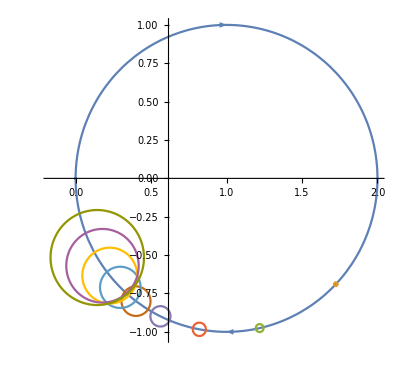

```mathematica
Show[p21,p22,PlotRange->All]
```

```mathematica
(* iii) Plot the Perron-Frobenius eigenvalue for w € [0, 1000] rad/s *)
```

```mathematica
Gjw=Gs/.s->(w I);
```

```mathematica
MatrixForm[Gjw]
```

((3+ⅈ w)/((1+ⅈ w) (6+ⅈ w)) | 1/(1+6 ⅈ w)
(1+ⅈ w)/(100+11 ⅈ w-w^2) | 2/(1+2 ⅈ w))

```mathematica
M=Abs[Gjw];
```

```mathematica
MatrixForm[M]
```

(Abs[(3+ⅈ w)/((1+ⅈ w) (6+ⅈ w))] | 1/Abs[1+6 ⅈ w]
Abs[(1+ⅈ w)/(100+11 ⅈ w-w^2)] | 2/Abs[1+2 ⅈ w])

```mathematica
Omega={{M[[1,1]],0},{0,M[[2,2]]}};
```

```mathematica
MatrixForm[Omega]
```

(Abs[(3+ⅈ w)/((1+ⅈ w) (6+ⅈ w))] | 0
0 | 2/Abs[1+2 ⅈ w])

```mathematica
Mnorm=Inverse[Omega].M;
```

```mathematica
MatrixForm[Mnorm]
```

(1 | 1/(Abs[(3+ⅈ w)/((1+ⅈ w) (6+ⅈ w))] Abs[1+6 ⅈ w])
1/2 Abs[1+2 ⅈ w] Abs[(1+ⅈ w)/(100+11 ⅈ w-w^2)] | 1)

```mathematica
lpf001=Eigenvalues[Mnorm/.w->(0.01)]
```

{1.09992,0.900075}

```mathematica
lpf01=Eigenvalues[Mnorm/.w->(0.1)]
```

{1.09396,0.906038}

```mathematica
lpf1=N[Eigenvalues[Mnorm/.w->(1)]]
```

{1.08425,0.915746}

```mathematica
lpf10=N[Eigenvalues[Mnorm/.w->(10)]]
```

{1.41367,0.586326}

```mathematica
lpf100=N[Eigenvalues[Mnorm/.w->(100)]]
```

{1.40935,0.590653}

```mathematica
lpf1000=N[Eigenvalues[Mnorm/.w->(1000)]]
```

{1.40826,0.591741}

```mathematica
(* |l1|>=|l2| then lpf > l2 *)
```

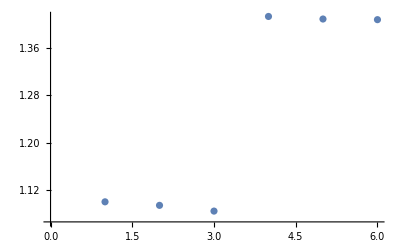

```mathematica
pl=ListPlot[{{1,lpf001[[1]]},{2,lpf01[[1]]},{3,lpf1[[1]]},{4,lpf10[[1]]},{5,lpf100[[1]]},{6,lpf1000[[1]]}}]
```

```mathematica
li=Eigenvalues[Mnorm];
```

```mathematica
lpf=li[[2]];
```

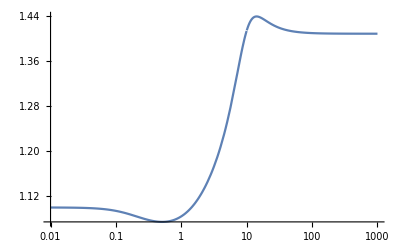

```mathematica
LogLinearPlot[lpf,{w,0.01,1000}]
```

```mathematica
(* iv) Design a Perron-Frobenius precompensator for w=0 *)
```

```mathematica
lpf0=N[Eigenvalues[Mnorm/.w->(0)]]
```

{1.1,0.9}

```mathematica
Kp={{lpf0[[1]],0},{0,lpf0[[2]]}};
```

```mathematica
MatrixForm[Kp]
```

(1.1 | 0
0 | 0.9)

```mathematica
(* v) Plot the entries of the Perron-Frobenius eigenvector for w €[0,1000] rad/s *)
```

```mathematica
vpf001=Eigenvectors[Mnorm/.w->(0.01)]
```

{{0.99875,0.0499875},{-0.99875,0.0499875}}

```mathematica
vpf01=Eigenvectors[Mnorm/.w->(0.1)]
```

{{0.998516,0.0544587},{-0.998516,0.0544587}}

```mathematica
vpf1=N[Eigenvectors[Mnorm/.w->(1)]]
```

{{5.30789,1.},{-5.30789,1.}}

```mathematica
vpf10=N[Eigenvectors[Mnorm/.w->(10)]]
```

{{0.452218,1.},{-0.452218,1.}}

```mathematica
vpf100=N[Eigenvectors[Mnorm/.w->(100)]]
```

{{0.407722,1.},{-0.407722,1.}}

```mathematica
vpf1000=N[Eigenvectors[Mnorm/.w->(1000)]]
```

{{0.408243,1.},{-0.408243,1.}}

```mathematica
ev001=0.0499875/0.99875;
```

```mathematica
ev01=0.0544587/0.998516;
```

```mathematica
ev1=1/5.30789;
```

```mathematica
ev10=1/0.452218;
```

```mathematica
ev100=1/0.407722;
```

```mathematica
ev1000=1/0.408243;
```

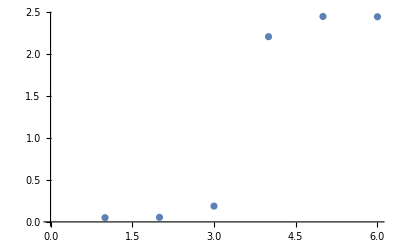

```mathematica
pv=ListPlot[{{1,ev001},{2,ev01},{3,ev1},{4,ev10},{5,ev100},{6,ev1000}}]
```

```mathematica
(* where x1=10^-2, x2=10^-1, x3=10^0, x4=10^1, x5=10^2, x6=10^3 *)
```

```mathematica
(* viii) Plot again the Nyquist array including the Gershgorin circles with the criteria of row dominance for the system and the precompensator in series connection *)
```

```mathematica
Qs = Inverse[Qinv];
```

```mathematica
QIw=Qs/.s->(w I);
```

```mathematica
f1w={Re[QIw[[1,1]]]+Abs[QIw[[1,2]]] Cos[t],Im[QIw[[1,1]]]+Abs[QIw[[1,2]]]  Sin[t]};
```

```mathematica
f11=f1w/.w->0.0;
```

```mathematica
f12=f1w/.w->0.2;
```

```mathematica
f13=f1w/.w->0.4;
```

```mathematica
f14=f1w/.w->0.6;
```

```mathematica
f15=f1w/.w->0.8;
```

```mathematica
f16=f1w/.w->1.0;
```

```mathematica
f17=f1w/.w->1.2;
```

```mathematica
f18=f1w/.w->1.4;
```

```mathematica
f19=f1w/.w->1.6;
```

```mathematica
f110=f1w/.w->1.8;
```

```mathematica
p11=NyquistPlot[Qs[[1,1]]];
```

```mathematica
p12=ParametricPlot[{f11,f12,f13,f14,f15,f16,f17,f18,f19,f110},{t,0,2 Pi}];
```

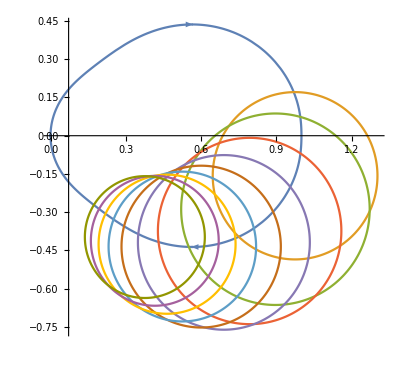

```mathematica
Show[p11,p12,PlotRange->All]
```

```mathematica
(* Nyquist Array Plot for element {1,2} *)
```

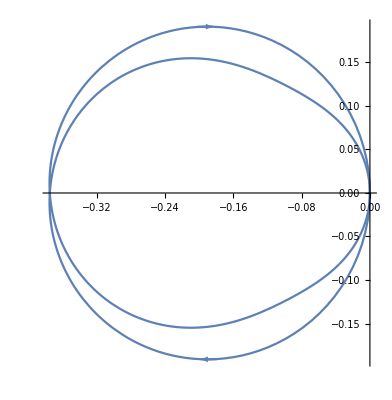

```mathematica
NyquistPlot[Qs[[1,2]]]
```

```mathematica
(* Nyquist Array Plot for element {2,1} *)
```

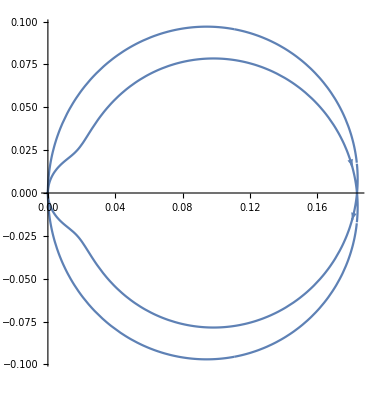

```mathematica
NyquistPlot[Qs[[2,1]]]
```

```mathematica
(* Nyquist Array Plot for element {2,2}, second diagonal *)
```

```mathematica
(* f2 = x2 + r2 Cos[t], y2 + r2 Sin[t] *)
```

```mathematica
(* x2 = Re[G22(jw)], y2 = Im[G22(jw)], r2 = dR2, dR2 = |q21(jw)| *)
```

```mathematica
f2w={Re[QIw[[2,2]]]+Abs[QIw[[2,1]]] Cos[t],Im[QIw[[2,2]]]+Abs[QIw[[2,1]]]  Sin[t]};
```

```mathematica
f21=f2w/.w->0.0;
```

```mathematica
f22=f2w/.w->0.2;
```

```mathematica
f23=f2w/.w->0.4;
```

```mathematica
f24=f2w/.w->0.6;
```

```mathematica
f25=f2w/.w->0.8;
```

```mathematica
f26=f2w/.w->1.0;
```

```mathematica
f27=f2w/.w->1.2;
```

```mathematica
f28=f2w/.w->1.4;
```

```mathematica
f29=f2w/.w->1.6;
```

```mathematica
f210=f2w/.w->1.8;
```

```mathematica
p21=NyquistPlot[Qs[[2,2]]];
```

```mathematica
p22=ParametricPlot[{f21,f22,f23,f24,f25,f26,f27,f28,f29,f210},{t,0,2 Pi}];
```

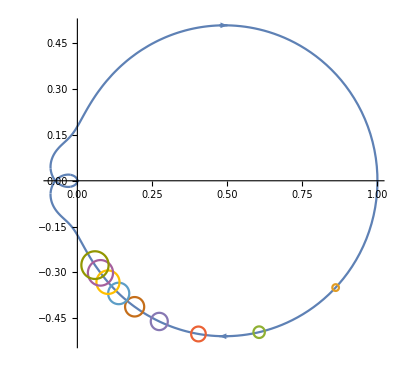

```mathematica
Show[p21,p22,PlotRange->All]
```